Wolfram Online Mini Campus. Part 1

Instagram Posts  
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 1

Parametric Plot

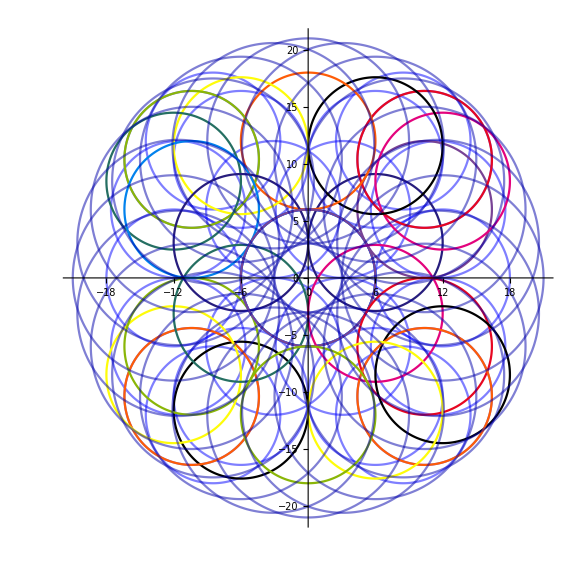

```mathematica
r1=6; r2=9; R=12; n=24; 
x=r1*Cos[t]-R*Cos[2i*π/n]; y=r1*Sin[t]-R*Sin[4i*π/n];
u=r2*Cos[t]-R*Cos[2i*π/n]; v=r2*Sin[t]-R*Sin[2i*π/n];
p1=ParametricPlot[Evaluate[Table[{x,y},{i,24}]],{t,0,2π},PlotStyle->Directive[Opacity[0.5],Blue]];
p2=ParametricPlot[Evaluate[Table[{y,x},{i,24}]],{t,0,2π},PlotStyle->ColorData[3,"ColorList"]];
p3=ParametricPlot[Evaluate[Table[{u,v},{i,24}]],{t,0,2π},PlotStyle->Directive[Opacity[0.5],Darker[Blue]]];
Show[p1,p2,p3,PlotRange->{{-21,21},{-21,21}},ImageSize->Large]
```

Interactive Polar Plot
https://reference.wolfram.com/language/tutorial/IntroductionToManipulate.html

```mathematica
m1=Manipulate[PolarPlot[Evaluate[Table[(i*t+k/5)*Log[t/5],{k,0,9}]],{t,0,2π},
                               PlotStyle->ColorData[n,"ColorList"],GridLines->Automatic,                                          
              PlotRange->{{-14,5},{-7,2}},ImageSize->Large],{i,1,n},{n,Range[1,24,1]}]
```

```mathematica
cloudm1=CloudDeploy[m1,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/6ae11dd1-f4b7-42c1-9c50-9caa96c9ad60]

```mathematica
EmbedCode[cloudm1]
(*It could be [%N] where N is the number of cell input*)
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | [Download Code](https://www.wolframcloud.com/obj/safuolga/cloudembed-e17.html)
<iframe src="https://www.wolframcloud.com/obj/6ae11dd1-f4b7-42c1-9c50-9caa96c9ad60?_embed=iframe" width="600" height="800"></iframe>

Unicode Characters

```mathematica
Print[CharacterRange["♔","♟"]]; Print[CharacterRange["α","ω"]]
```

{♔,♕,♖,♗,♘,♙,♚,♛,♜,♝,♞,♟}

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,ς,σ,τ,υ,φ,χ,ψ,ω}

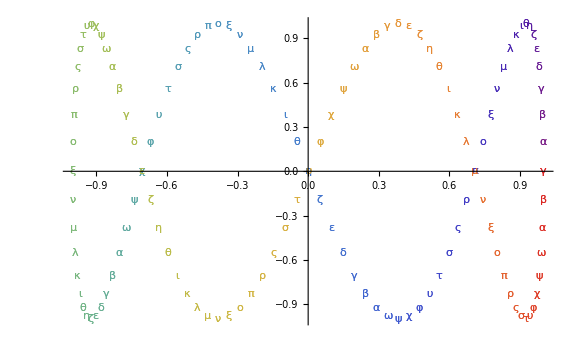

```mathematica
data=Table[{Cos[n*π/64],Sin[n*π/16]},{n,128}];
ListPlot[List /@ data,PlotMarkers ->ToString /@ CharacterRange["α","ω"],PlotStyle->"Rainbow",ImageSize->Large]
```

```mathematica
Manipulate[Permutations[Take[FromCharacterCode[{{945},{946},{947},{948},{949}}],ch]],{ch,Range[1,5,1]}]
```

Built-In Datasets
https://datarepository.wolframcloud.com/resources/Sample-Data-Boston-Homes

```mathematica
boston=ResourceData["Sample Data: Boston Homes"]; boston[1,All]
```

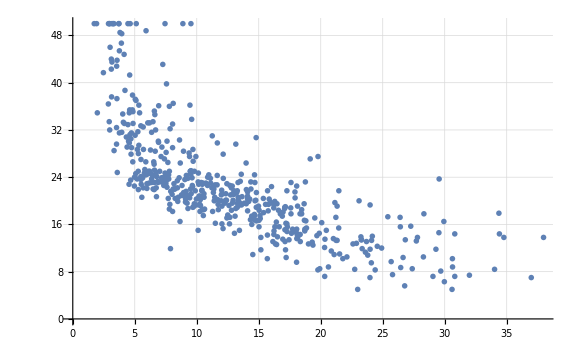

```mathematica
ListPlot[boston[All,{"LSTAT","MEDV"}],GridLines->Automatic,ImageSize->Large,
                   PlotMarkers -> Thread[{ChartElementData["EmptyMarkers"][[All, 1]],.01}]]
```

```mathematica
p=Predict[boston[All,"RM"]->boston[All,"MEDV"], Method -> "LinearRegression"]
Information[p]
```

PredictorFunction[…]

Predictor information
Data type | Numerical
Standard deviation | 6.46 ± 0.49
Method | LinearRegression
Single evaluation time | 1.96 ms/example
Batch evaluation speed | 180. examples/ms
Loss | 3.31 ± 0.11
Model memory | 260. kB
Training examples used | 506 examples
Training time | 1.29 s
 |

```mathematica
p1=Plot[{p[x],p[x] + StandardDeviation[p[x, "Distribution"]],
                   p[x] - StandardDeviation[p[x, "Distribution"]]},{x, 3, 9},
                   PlotStyle -> {Blue, Gray, Gray},Filling -> {2 -> {3}},Exclusions -> False,
                   PerformanceGoal -> "Speed",PlotLegends -> {"Prediction", "Confidence Interval"}];
p2=ListPlot[boston[All,{"RM","MEDV"}], PlotStyle -> Red, PlotLegends -> {"Data"}];
Show[p1,p2,GridLines->Automatic,ImageSize->Large]
```

-Graphics-

https://datarepository.wolframcloud.com/resources/Sample-Data-Birth-Weight-Risk

```mathematica
bwr=ResourceData["Sample Data: Birth Weight Risk"]; bwr[1;;5]
```

```mathematica
h1=Histogram[bwr[Select[#Smoker==False&], "BWT"],50,
                                 ChartElementFunction -> "GlassRectangle",ChartStyle -> "Rainbow"];
h2=Histogram[bwr[Select[#Smoker==True&], "BWT"],30,
                                ChartElementFunction -> "GlassRectangle",ChartStyle ->"Pastel"];
Show[h1,h2,ImageSize->Large, PlotLabel-> {"Birth Weight for Smokers vs Non-Smokers"}]
```

-Graphics-

HTML Code Fragments

```mathematica
EmbeddedHTML[
"<style>@import url('https://fonts.googleapis.com/css?family=Ewert&effect=3d');</style> <svg width='400' height='80'> <linearGradient id='b' x2='0' y2='100%'> <stop offset='0' stop-color='#aaa' stop-opacity='.1'/> <stop offset='1' stop-opacity='.5'/> </linearGradient> <clipPath id='a'><rect width='400' height='80' rx='20'/></clipPath> <g clip-path='url(#a)'><path fill='#ff3636' d='M0 0h280v80H0z'/> <path fill='#3636ff' d='M280 0h120v80H280z'/> <path fill='url(#b)' d='M0 0h280v80H0z'/></g> <g style='fill:#fff; font-family:Ewert; font-size:35' class='font-effect-3d'> <text x='10' y='45'>in progress</text><text x='320' y='45'>%</text></g> </svg>"]
```

Null<style>@import url('https://fonts.go…xt x='320' y='45'>%</text></g> </svg><style>@import url('https://fonts.googleapis.com/css?family=Ewert&effect=3d');</style> <svg width='400' height='80'> <linearGradient id='b' x2='0' y2='100%'> <stop offset='0' stop-color='#aaa' stop-opacity='.1'/> <stop offset='1' stop-opacity='.5'/> </linearGradient> <clipPath id='a'><rect width='400' height='80' rx='20'/></clipPath> <g clip-path='url(#a)'><path fill='#ff3636' d='M0 0h280v80H0z'/> <path fill='#3636ff' d='M280 0h120v80H280z'/> <path fill='url(#b)' d='M0 0h280v80H0z'/></g> <g style='fill:#fff; font-family:Ewert; font-size:35' class='font-effect-3d'> <text x='10' y='45'>in progress</text><text x='320' y='45'>%</text></g> </svg>